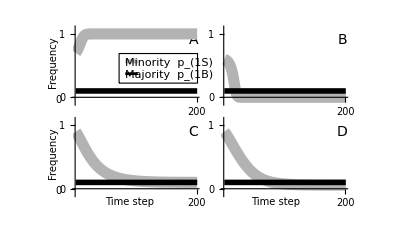

~/Fig3_onepatch.pdf

```mathematica
(*Makes figure 4 in appendix: norm frequency trajectories for one-patch model*)


Clear[wik,wnik, Rk, Rik, Vk, Vik, boundsim,a,m,d,g,mu];

(*simulation function*)
boundsim[
pg1init_,(*(vector) group 1: norm 0, norm 1*)
pg2init_,(*(vector) group 2: norm 0, norm 1*)
tmax_,(*# sims*)
a_,(*prob of assorting on marker*)
m_,(*(vector) proportion of each group that is visitors*)
d_,(*(matrix) relative group sizes: how many times bigger the row group is than the column group*)
g_,(*(vector) inter-ethnic coordination payoff bonus for each group*)
mu_ (*effect of a payoff difference on copying*)
]:=Module[{},

(*intialize vectors and matrices*)
p1={pg1init[[1]], pg2init[[1]]}; (*norm 0 in both groups*)
p2={pg1init[[2]], pg2init[[2]]}; (*norm 1 in both groups*)
matg1all={pg1init}; (*matrix holding norm freqs for group 1*)
matg2all={pg2init};
fitg1={1,1}; (*fitness of norms in group 1*)
fitg2={1,1};
fitg1all={fitg1}; (*matrix holding norm fitnesses for group 1*)
fitg2all={fitg2};

(*generalized fitness*)
Rk=(1-mk)+dnk*mnk;
Rik=pik*(1-mk)+pink*dnk*mnk;

fitnessik=a*((1-mk)*1/Rik*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1));


(*new phenotype freqs after copying*)
pikprime=pik+pik*pnik*mu*(wik-wnik);


(*simulation*)
For    [t=1,t<=tmax,t++,

(*update norm frequencies for the two groups*)
p1k=p1;
p2k=p2;

k=1; (*just interested in resident interaction pool of minority group*)
nk=2;


(*phenotype fitnesses*)

If[p1k=={0,0},
w1k=0,
w1k=fitnessik/.{
dnk->d[[nk,k]],gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p1k[[k]],pink->p1k[[nk]]
}
];

If[p1k=={0,0},
w1nk=0,
w1nk=fitnessik/.{
dnk->d[[k,nk]],gk->g[[nk]],
mk->m[[nk]],mnk->m[[k]],
pik->p1k[[nk]],pink->p1k[[k]]
}
];

If[p2k=={0,0},
w2k=0,
w2k=fitnessik/.{
dnk->d[[nk,k]],gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p2k[[k]],pink->p2k[[nk]]
}
];

If[p2k=={0,0},
w2nk=0,
w2nk=fitnessik/.{
dnk->d[[k,nk]],gk->g[[nk]],
mk->m[[nk]],mnk->m[[k]],
pik->p2k[[nk]],pink->p2k[[k]]
}
];


(*Recursion*)
p1kprime=pikprime /.
{pik->p1k[[k]],
pnik->p2k[[k]],
wik->w1k,
wnik->w2k};

p2kprime=1-p1kprime;


(*update phenotype and fitness matrices*)

p1={p1kprime,pg2init[[1]]}; (*update freq of norm 0 for group 1*)
p2={p2kprime,pg2init[[2]]};(*update freq of norm 1 for group 1*)
fitg1={w1k,w2k};


(*accumulate phenotype freqs and fitnesses across sims*)
matg1all=Join[matg1all,{{p1[[1]],p2[[1]]}}];
matg2all=Join[matg2all,{{p1[[2]],p2[[2]]}}];
fitg1all=Join[fitg1all, {fitg1}];

](*for t*)

];(*boundsim*)




(*Figure 3: plotting norm frequency trajectories*)

(*A*************************no assortment, norm 0 majority*******************************)

boundsim[
pg1init={0.7,0.3},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0, (*prob of assorting on marker*)
m={0,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.5,0},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];


(*
Print["Ending freq of norm 0 in both groups: ", p1,"

Matrices of norm freqs in each group: 
",
matg1all //MatrixForm,
matg2all //MatrixForm, "

Matrices of fitnesses of norms in each group:
",
fitg1all//MatrixForm,
fitg2all//MatrixForm
] 
*)

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)



(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3a=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,Black},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0"},{1,"1"}}}
];
(*
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)



(*B****************no assortment, norm 0 lower freq*************************)
boundsim[
pg1init={0.6,0.4},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0, (*prob of assorting on marker*)
m={0,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.5,0},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];


(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)


(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3b=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,White},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0",{0,0}},{1,"1",{0,0}}}}
];




(*C************************perfect assortment*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=1, (*prob of assorting on marker*)
m={0,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.5,0},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3c=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,Black},
Ticks->{{{100,""},{200,"200"}},{{0,"0"},{1,"1"}}}
];


(*D************************high assortment*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.95, (*prob of assorting on marker*)
m={0,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.5,0},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3d=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,White},
Ticks->{{{100,""},{200,"200"}},{{0,"0",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(****************************************assemble plots into Fig 3*)
Fig3=Panel[
GraphicsGrid[
{{f3a,f3b},{f3c,f3d}},

Spacings->{
{
Scaled[0.4],
Scaled[0],
Scaled[0.2]
},
{
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["A",14],{380,-45}],
Inset[Style["B",14],{740,-45}],
Inset[Style["C",14],{380,-270}],
Inset[Style["D",14],{740,-270}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-100}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-320}],
Inset[Style["Time step",10],{225,-440}],
Inset[Style["Time step",10],{580,-440}],
Inset[Style["0",10],{54,-190}],
Inset[Style["0",10],{54,-412}],

x=40;
y=0;
{EdgeForm[Thin],White,Rectangle[{160+x,-78+y},{350+x,-150+y}]},
Inset[Style["Minority ",10]Style[Subscript[Style["p",Italic,10],Style["1S",8]],Italic,10],{280+x,-100+y}],
Inset[Style["Majority ",10]Style[Subscript[Style["p",Italic,10],Style["1B",8]],Italic,10],{280+x,-130+y}],
{AbsoluteThickness[3],GrayLevel[0.7],Line[{{175+x,-97+y},{205+x,-97+y}}]},
{AbsoluteThickness[2],Black,Line[{{175+x,-127+y},{205+x,-127+y}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["~/Fig3_onepatch.pdf",Fig3,"PDF"]
```